```mathematica
Z=Cos[n(α+β)]; X=Cos[α]; Y=Sin[α];
```

```mathematica
ParametricPlot3D[{{X,Y,Z 0.4}/.{n->4,β->0.3 2 π},{X,Y,0}},{α,0,2 π}]
```

-Graphics3D-

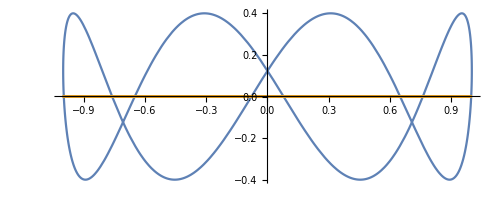

```mathematica
ParametricPlot[{{X,Z 0.4}/.{n->4,β->0.3 2 π},{X,0}},{α,0,2 π}]
```

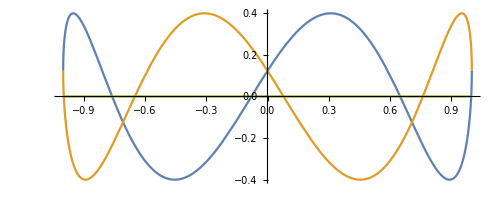

```mathematica
ParametricPlot[{{X,Z 0.4}/.{n->4,β->0.3 2 π},{X,Z 0.4}/.{α->-α,n->4,β->0.3 2 π},{X,0}},{α,0,π}]
```

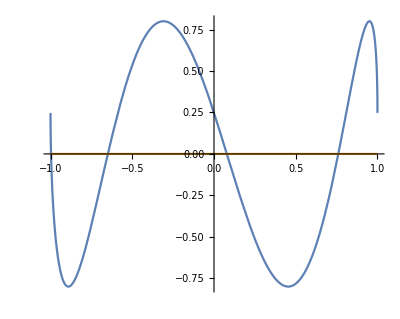

```mathematica
ParametricPlot[{{X,(Z+Z/.{α->-α})0.4}/.{n->4,β->0.3 2 π},{X,0}},{α,0,π}]
```

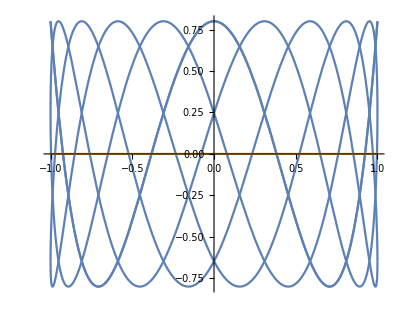

```mathematica
ParametricPlot[{Table[{X,(Z+Z/.{α->-α})0.4}/.{n->4},{β,0,π,.2 π}],{X,0}},{α,0,π}]
```

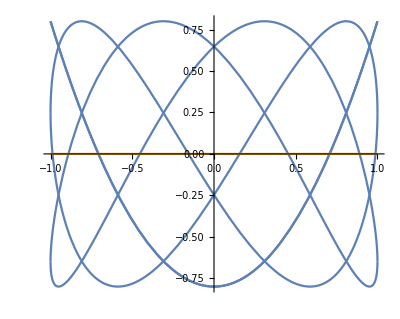

```mathematica
ParametricPlot[{Table[{X,(Z+Z/.{α->-α})0.4}/.{n->2},{β,0,π,.2 π}],{X,0}},{α,0,π}]
```

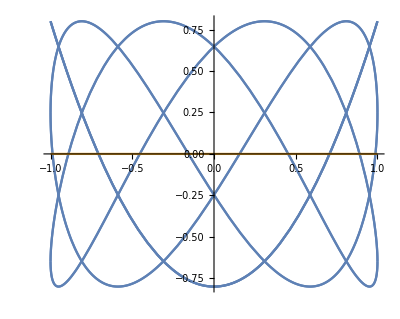

```mathematica
ParametricPlot[{Table[{X,(Z+Z/.{α->-α,β->-β})0.4}/.{n->2},{β,0,2 π,.2 π}],{X,0}},{α,0,π}]
```

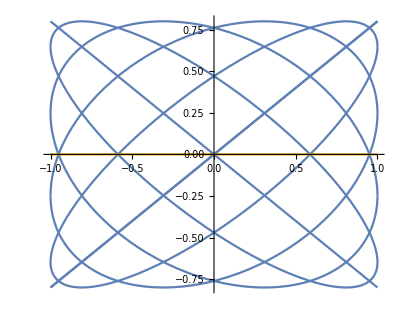

```mathematica
ParametricPlot[{Table[{X,(Z+Z/.{α->-α,β->-β})0.4}/.{n->1},{β,0,2 π,.2 π}],{X,0}},{α,0,π}]
```